# © Kamal K. Barley, Andreas Ruffing, and Sergei K. Suslov “Oganesson versus Uranium Hydrogen-like Ions (from the Viewpoint of Old Quantum Mechanics”)

arXiv:2509.06249v2[quant-ph] 15 Sept 2025

https://arxiv.org/pdf/2509.06249

(Last modified/executed on September  23, 2025;  8:15 AM Arizona time.)

```mathematica
SetDirectory[NotebookDirectory[]];
```

0.576207

0.930786

0.0249872

{0.00172947,0.0482449}

4.6212

10.9044

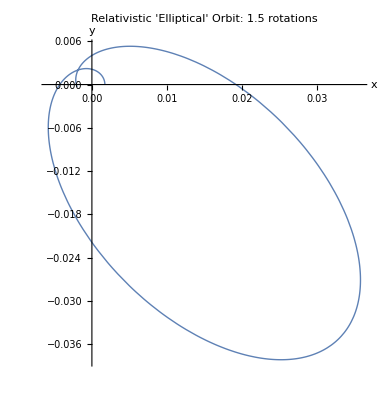

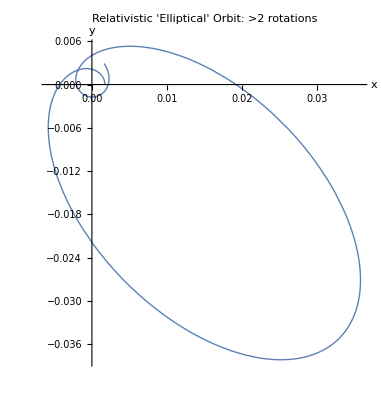

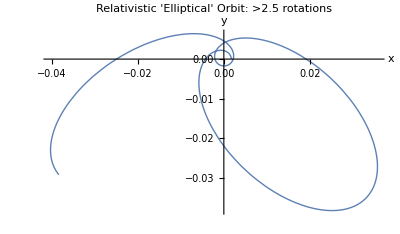

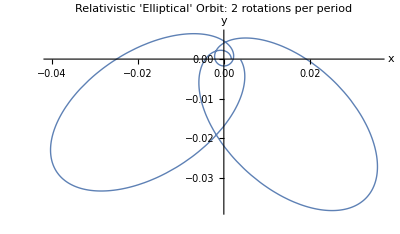

```mathematica
(*---Constants and Setup---*)(*Pretty print subscript-style variables for display only*)MakeBoxes[nt,StandardForm]:=SubscriptBox["n","t"]
MakeBoxes[nr,StandardForm]:=SubscriptBox["n","r"]

(*Physical constants*)
Z=112; (*Atomic number of Copernicium,Cn*)
α=1/137.036; (*Fine structure constant*)

(*Quantum numbers*)
ntVal=1;
nrVal=1;

(*---Define symbolic formulas as functions---*)

(*Eq.(3.19)*)
ωFunc[nt_]:=Sqrt[nt^2-Z^2 α^2]/nt

(*Eq.(3.20)*)
ϵFunc[nt_,nr_]:=Sqrt[nr] Sqrt[(nr+2 Sqrt[nt^2-Z^2 α^2])]/(nr+Sqrt[nt^2-Z^2 α^2])

(*Eq.(3.21)*)
aFunc[nt_,nr_]:=((nr+Sqrt[nt^2-Z^2 α^2]) Sqrt[Z^2 α^2+(nr+Sqrt[nt^2-Z^2 α^2])^2])/Z

(*---Compute numeric values---*)

ωVal=ωFunc[ntVal]//N
ϵVal=ϵFunc[ntVal,nrVal]//N
aVal=aFunc[ntVal,nrVal]//N
{rMin=aVal*(1-ϵVal) //N, rMax=aVal*(1+ϵVal) //N}
DeltaTheta=2*Pi*((1/ωVal) -1) //N
PeriodTheta=2*Pi*(1/ωVal)  //N

(*---Define relativistic radial orbit r(t) from Eq.(3.9)---*)
r[t_]:=(aVal (1-ϵVal^2))/(1+ϵVal Cos[ωVal t])

 PolarPlot[r[t],{t,0,0.88*PeriodTheta},PlotLabel->"Relativistic 'Elliptical' Orbit: 1.5 rotations",AxesLabel->{"x","y"},PlotRange->All,PlotStyle->Thick]
PolarPlot[r[t],{t,0,1.25*PeriodTheta},PlotLabel->"Relativistic 'Elliptical' Orbit: >2 rotations",AxesLabel->{"x","y"},PlotRange->All,PlotStyle->Thick]
PolarPlot[r[t],{t,0,1.5*PeriodTheta},PlotLabel->"Relativistic 'Elliptical' Orbit: >2.5 rotations",AxesLabel->{"x","y"},PlotRange->All,PlotStyle->Thick]
PolarPlot[r[t],{t,0,1.725*PeriodTheta},PlotLabel->"Relativistic 'Elliptical' Orbit: 2 rotations per period",AxesLabel->{"x","y"},PlotRange->All,PlotStyle->Thick]
```

```mathematica
Export["CoperniciumIon111.pdf",%]
```

CoperniciumIon111.pdf

```mathematica
(*Animation in Cartesian Coordinates*)Manipulate[ParametricPlot[{r[t] Cos[t],r[t] Sin[t]},{t,0,tMax},PlotStyle->{Blue,Thick},AxesLabel->{"x","y"},PlotLabel->Style["Relativistic Elliptical Orbit(Animated, Cartesian)",14,Bold],PlotRange->{{-rMax,rMax},{-rMax,rMax}},(*Fixed range ensures full visibility from Subscript[r, min] to Subscript[r, max]*)AspectRatio->1,PlotPoints->1000,PerformanceGoal->"Quality"],{tMax,0.01,24 Pi,Appearance->"Labeled"}]
```

Summary: 
In the above animation of the relativistic Kepler motion of an electron in hydrogen-like Copernicium, Cn, when Z=112, the nucleus is situated  in the fixed focus at the origin.  For this quantum state, we choose n_r=nr=1 and n_θ=nt=1 in the fine structure formula (3.18). By (3.19)-(3.21), one gets: ω= 0.576207,  ϵ=0.930786, and a=0.0249872, in Bohr’s atomic units. 
The perihelion and aphelion move along two concentric circles around the nucleus with radii:   r_min=a (1-ϵ)=0.00172947 and r_max=a (1+ϵ)=0.0482449, respectively.  In the animation, the geometrical loci of the successive perihelia and aphelia, the outer and inner envelopes of the orbit, see Figure 3, are not shown for simplicity.
Rotation of the ellipse over one period is given by Δθ=2π(1/ω-1)=4.6212.  At the point of self-intersection one gets, approximately,  r[2.3799243523877007`]=r[8.52445631673413`]=0.00281928 with  r[2.3799243523877007`]-r[8.52445631673413`]=-1.73472×10^-18.

```mathematica
r[t]
```

0.00333924/(1+0.930786 Cos[0.576207 t])

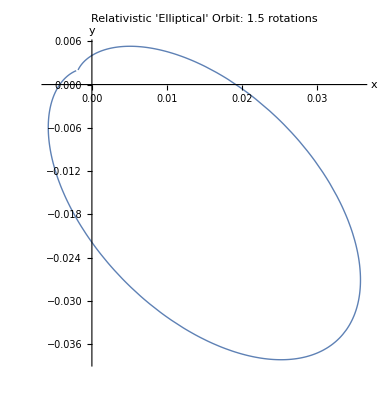

```mathematica
PolarPlot[r[t],{t,0.22*PeriodTheta,0.788*PeriodTheta},PlotLabel->"Relativistic 'Elliptical' Orbit: 1.5 rotations",AxesLabel->{"x","y"},PlotRange->All,PlotStyle->Thick]
```

```mathematica
{0.22*PeriodTheta,0.788*PeriodTheta}
```

{2.39896,8.59265}

```mathematica
r[2.398963747206803]-r[8.592651967268004]
```

0.000106539

```mathematica
8.592651967268004/2.398963747206803
```

3.58182

```mathematica
FindRoot[r[t]-r[3.5818181818181825*t]==0,{t,2.4}]
```

{t→2.37992}

```mathematica
3.5818181818181825*2.3799243523877007
```

8.52446

```mathematica
r[2.3799243523877007]-r[8.52445631673413]
```

-1.73472×10^-18

```mathematica
{r[2.3799243523877007],r[8.52445631673413]}
```

{0.00281928,0.00281928}

```mathematica
ωVal*(2.3799243523877007+8.52445631673413)/2//N
```

3.14159

```mathematica
3.1415926535897927-Pi//N
```

-4.44089×10^-16